# Analytical Writhed Magnetic Flux Rope Model (Figures)

```mathematica
RFrenetSerretEqs = {
γ'[s]->t[s]l[s],
t'[s] -> κ[s]n[s]l[s],
n'[s]->-κ[s]t[s]l[s]+ τ[s]b[s]l[s],
b'[s]->-τ[s]n[s]l[s]
};

RFrenetSerretGeometry = {
t[s]⊗t[s] -> 1,
n[s]⊗n[s] -> 1,
b[s]⊗b[s] -> 1,

t[s]⊗n[s] -> 0,
n[s]⊗t[s] -> 0,
t[s]⊗b[s] -> 0,
b[s]⊗t[s] -> 0,
n[s]⊗b[s] -> 0,
b[s]⊗n[s] -> 0,

t[s]×t[s] -> 0,
n[s]×n[s] -> 0,
b[s]×b[s] -> 0,

t[s]×n[s] -> b[s],
n[s]×b[s] -> t[s],
b[s]×t[s] -> n[s],
n[s]×t[s] ->-b[s],
t[s]×b[s] -> -n[s],
b[s]×n[s] -> -t[s]
};

RFrenetSerretVariables ={
r ∈ PositiveReals,
σ ∈ PositiveReals,
l[s]∈ PositiveReals,
κ[s] ∈ PositiveReals,
τ[s]∈ Reals,

γ[s]∈ Vectors[3, Reals],
t[s]∈ Vectors[3, Reals],
t'[s]∈ Vectors[3, Reals],
n[s]∈ Vectors[3, Reals],
n'[s]∈ Vectors[3, Reals],
b'[s]∈ Vectors[3, Reals],
b'[s]∈ Vectors[3, Reals]
};

FSv[r_, s_,φ_] :=γ[s] - r σ n[s] Cos[φ]-r σ  b[s]Sin[φ];

Subscript[FSϵ, r][r_,s_,φ_]:=D[FSv[r,s,φ],r]/. RFrenetSerretEqs
Subscript[FSϵ, s][r_,s_,φ_]:=D[FSv[r,s,φ],s]/.RFrenetSerretEqs // FullSimplify
Subscript[FSϵ, φ][r_,s_,φ_]:=D[FSv[r,s,φ],φ]/.RFrenetSerretEqs // FullSimplify
Subscript[FSg, rr][r_,s_,φ_]:=TensorExpand[Subscript[FSϵ, r][r,s,φ]⊗Subscript[FSϵ, r][r,s,φ] , Assumptions->RFrenetSerretVariables] /. RFrenetSerretGeometry // FullSimplify
Subscript[FSg, ss][r_,s_,φ_]:=TensorExpand[Subscript[FSϵ, s][r,s,φ]⊗Subscript[FSϵ, s][r,s,φ] , Assumptions->RFrenetSerretVariables] /. RFrenetSerretGeometry // FullSimplify
Subscript[FSg, φφ][r_,s_,φ_]:=TensorExpand[Subscript[FSϵ, φ][r,s,φ]⊗Subscript[FSϵ, φ][r,s,φ] , Assumptions->RFrenetSerretVariables] /. RFrenetSerretGeometry // FullSimplify
Subscript[FSg, rs][r_,s_,φ_] :=TensorExpand[Subscript[FSϵ, r][r,s,φ]⊗Subscript[FSϵ, s][r,s,φ] , Assumptions->RFrenetSerretVariables] /. RFrenetSerretGeometry // FullSimplify
Subscript[FSg, rφ][r_,s_,φ_] :=TensorExpand[Subscript[FSϵ, r][r,s,φ]⊗Subscript[FSϵ, φ][r,s,φ] , Assumptions->RFrenetSerretVariables] /. RFrenetSerretGeometry // FullSimplify
Subscript[FSg, sφ][r_,s_,φ_] :=TensorExpand[Subscript[FSϵ, s][r,s,φ]⊗Subscript[FSϵ, φ][r,s,φ] , Assumptions->RFrenetSerretVariables] /. RFrenetSerretGeometry // FullSimplify
Subscript[FSg, ij][r_,s_,φ_]:={{Subscript[FSg, rr][r,s,φ],Subscript[FSg, rs][r,s,φ],Subscript[FSg, rφ][r,s,φ]},{Subscript[FSg, rs][r,s,φ],Subscript[FSg, ss][r,s,φ],Subscript[FSg, sφ][r,s,φ]},{Subscript[FSg, rφ][r,s,φ],Subscript[FSg, sφ][r,s,φ],Subscript[FSg, φφ][r,s,φ]}};
FSsqg[r_, s_, φ_] := FullSimplify[Sqrt[Det[Subscript[FSg, ij][r,s,φ]] // FullSimplify], Assumptions->RFrenetSerretVariables] /. Sqrt[x_^2 y_^2] :> x y/. Sqrt[x_^2 ] :> x 

Subscript[FSh, r][r_, s_, φ_] := FullSimplify[Sqrt[Subscript[FSg, rr][r,s,φ]], Assumptions->RFrenetSerretVariables]
Subscript[FSh, s][r_, s_, φ_] := FullSimplify[Sqrt[Subscript[FSg, ss][r,s,φ]], Assumptions->RFrenetSerretVariables]
Subscript[FSh, φ][r_, s_, φ_] := FullSimplify[Sqrt[Subscript[FSg, φφ][r,s,φ]], Assumptions->RFrenetSerretVariables]

Subscript[FSB, r][r_,s_,φ_]:=0
Subscript[FSB, s][r_,s_,φ_]:= -1/l[s]((Subscript[μ, 0] σ √(1-r^2 σ^2 κ[s]^2))/(1+r σ Cos[φ]  κ[s])^2+(Subscript[μ, 0]  σ Subscript[Â, 1][r,s,φ])/(1+r σ Cos[φ]  κ[s]))∑_(n=0)^Subscript[n, m] α[n]LegendreP[n, 2r-1] 
Subscript[FSB, φ][r_,s_,φ_]:=  (- Subscript[μ, 0])/(1+r σ Cos[φ]  κ[s])(∑_(m=0)^Subscript[m, m] β[m]LegendreP[m, 2r-1]) +(Subscript[μ, 0] σ(-(r σ Sin[φ] κ'[s])/(√(1-r^2 σ^2 κ[s]^2))+Integrate[D[Subscript[Â, 1][r,s,Subscript[φ, t]],s],{Subscript[φ, t], 0, φ}] (1+r σ Cos[φ] κ[s])))/(l[s](1+r σ Cos[φ] κ[s])^2)∑_(n=0)^Subscript[n, m] α[n]LegendreP[n, 2r-1] 

Subscript[FSB, D][r_,s_,φ_]:=D[FSsqg[r,s,φ]Subscript[FSB, s][r,s,φ],s]+D[FSsqg[r,s,φ]Subscript[FSB, φ][r,s,φ],φ]
Subscript[FSJ, r][r_,s_,φ_]:= (D[Subscript[FSg, sφ][r,s,φ]Subscript[FSB, s][r,s,φ]+Subscript[FSg, φφ][r,s,φ]Subscript[FSB, φ][r,s,φ],s] - D[Subscript[FSg, ss][r,s,φ]Subscript[FSB, s][r,s,φ]+Subscript[FSg, sφ][r,s,φ]Subscript[FSB, φ][r,s,φ],φ]) /FSsqg[r, s, φ] / Subscript[μ, 0]
Subscript[FSJ, s][r_,s_,φ_]:= (D[Subscript[FSg, rs][r,s,φ]Subscript[FSB, s][r,s,φ]+Subscript[FSg, rφ][r,s,φ]Subscript[FSB, φ][r,s,φ],φ] - D[Subscript[FSg, sφ][r,s,φ]Subscript[FSB, s][r,s,φ]+Subscript[FSg, φφ][r,s,φ]Subscript[FSB, φ][r,s,φ],r]) /FSsqg[r, s, φ] / Subscript[μ, 0]
Subscript[FSJ, φ][r_,s_,φ_]:= (D[Subscript[FSg, ss][r,s,φ]Subscript[FSB, s][r,s,φ]+Subscript[FSg, sφ][r,s,φ]Subscript[FSB, φ][r,s,φ],r] - D[Subscript[FSg, rs][r,s,φ]Subscript[FSB, s][r,s,φ]+Subscript[FSg, rφ][r,s,φ]Subscript[FSB, φ][r,s,φ],s]) /FSsqg[r, s, φ] / Subscript[μ, 0]
Subscript[FSJ, D][r_,s_,φ_]:=D[FSsqg[r,s,φ]Subscript[FSJ, r][r,s,φ],r]+D[FSsqg[r,s,φ]Subscript[FSJ, s][r,s,φ],s]+D[FSsqg[r,s,φ]Subscript[FSJ, φ][r,s,φ],φ]

Subscript[FSF, r][r_,s_,φ_]:=Simplify[Inverse[Subscript[FSg, ij][r,s,φ]]][[1]][[1]]FSsqg[r, s, φ](Subscript[FSJ, s][r,s,φ]Subscript[FSB, φ][r,s,φ]-Subscript[FSJ, φ][r,s,φ]Subscript[FSB, s][r,s,φ])
Subscript[FSF, s][r_,s_,φ_]:=Simplify[Inverse[Subscript[FSg, ij][r,s,φ]]][[2]][[2]]FSsqg[r, s, φ](-Subscript[FSJ, r][r,s,φ]Subscript[FSB, φ][r,s,φ])+Simplify[Inverse[Subscript[FSg, ij][r,s,φ]]][[2]][[3]]FSsqg[r, s, φ](Subscript[FSJ, r][r,s,φ]Subscript[FSB, s][r,s,φ])
Subscript[FSF, φ][r_,s_,φ_]:=Simplify[Inverse[Subscript[FSg, ij][r,s,φ]]][[3]][[3]]FSsqg[r, s, φ](Subscript[FSJ, r][r,s,φ]Subscript[FSB, s][r,s,φ])+Simplify[Inverse[Subscript[FSg, ij][r,s,φ]]][[2]][[3]]FSsqg[r, s, φ](-Subscript[FSJ, r][r,s,φ]Subscript[FSB, φ][r,s,φ])

SetGeometryCylinder = {κ[s] -> 0, κ'[s] -> 0,κ''[s] -> 0,τ[s] -> 0,τ'[s] -> 0,τ''[s] -> 0,Derivative[0,1,0][x_][a_, b_, c_] :> 0, Derivative[0,2,0][x_][a_, b_, c_] :> 0};
SetGeometryTorus := {κ'[s] -> 0,κ''[s] -> 0,τ[s] -> 0,τ'[s] -> 0,τ''[s] -> 0,Derivative[0,1,0][x_][a_, b_, c_] :> 0, Derivative[0,2,0][x_][a_, b_, c_] :> 0};
SetZeroAFunc := {Subscript[Â, 1][r,s,p_]:> 0,Derivative[1,0,0][Subscript[Â, 1]][r,s,p_]:>0,Derivative[0,1,0][Subscript[Â, 1]][r,s,p_]:> 0,Derivative[0,0,1][Subscript[Â, 1]][r,s,p_]:> 0,Derivative[2,0,0][Subscript[Â, 1]][r,s,p_]:>0,Derivative[0,2,0][Subscript[Â, 1]][r,s,p_]:> 0,Derivative[0,0,2][Subscript[Â, 1]][r,s,p_]:> 0 ,Derivative[1,1,0][Subscript[Â, 1]][r,s,p_]:> 0,Derivative[1,2,0][Subscript[Â, 1]][r, s, y_] :> 0,Derivative[1,0,1][Subscript[Â, 1]][r, s, y_] :> 0}
SetAFuncTo[F_] := {Subscript[Â, 1][r,s,p_]:> F[r,s,p],Derivative[1,0,0][Subscript[Â, 1]][r,s,p_]:>D[F[r,s,p],r],Derivative[0,1,0][Subscript[Â, 1]][r,s,p_]:> D[F[r,s,p],s],Derivative[0,0,1][Subscript[Â, 1]][r,s,p_]:> D[F[r,s,p],p],Derivative[2,0,0][Subscript[Â, 1]][r,s,p_]:>D[F[r,s,p], {r,2}],Derivative[0,2,0][Subscript[Â, 1]][r,s,p_]:> D[F[r,s,p], {s,2}],Derivative[0,0,2][Subscript[Â, 1]][r,s,p_]:> D[F[r,s,p], {p, 2}],Derivative[1,1,0][Subscript[Â, 1]][r,s,p_]:> D[D[F[r,s,p],s],r],Derivative[1,2,0][Subscript[Â, 1]][r, s, y_] :> D[D[F[r,s,p],{s,2}],r],Derivative[1,0,1][Subscript[Â, 1]][r, s, y_] :> D[D[F[r,s,p],p],r]}

Bv[r_,s_,φ_]:= Subscript[FSϵ, s][r,s,φ]Subscript[FSB, s][r,s,φ]+Subscript[FSϵ, φ][r,s,φ]Subscript[FSB, φ][r,s,φ]
Jv[r_,s_,φ_]:= Subscript[FSϵ, r][r,s,φ]Subscript[FSJ, r][r,s,φ]+Subscript[FSϵ, s][r,s,φ]Subscript[FSJ, s][r,s,φ]+Subscript[FSϵ, φ][r,s,φ]Subscript[FSJ, φ][r,s,φ]
Fv[r_,s_,φ_]:= Subscript[FSϵ, r][r,s,φ]Subscript[FSF, r][r,s,φ]+Subscript[FSϵ, s][r,s,φ]Subscript[FSF, s][r,s,φ]+Subscript[FSϵ, φ][r,s,φ]Subscript[FSF, φ][r,s,φ]

LPCoeff[n_] := Integrate[Subscript[B, 0]/(1+Subscript[γ, 0]^2 r^2) LegendreP[n, 2r-1](2n+1), {r, 0, 1}, Assumptions->{Subscript[γ, 0]∈ Reals}] // Normal
ConfigGH = {
β[m_]:>Subscript[γ, 0] α[m],
Subscript[n, m]->12,Subscript[m, m]->12,
α[0] -> -LPCoeff[0],
α[1] -> -LPCoeff[1],
α[2] -> -LPCoeff[2],
α[3] -> -LPCoeff[3],
α[4] -> -LPCoeff[4],
α[5] -> -LPCoeff[5],
α[6] -> -LPCoeff[6],
α[7] -> -LPCoeff[7],
α[8] -> -LPCoeff[8],
α[9] -> -LPCoeff[9],
α[10] -> -LPCoeff[10],
α[11] -> -LPCoeff[11]
};
ConfigGH=Join[ConfigGH,Solve[∑_(n=0)^Subscript[n, m] (-1)^(1+n) (n+n^2) α[n]==0 //. ConfigGH,α[12]] // Flatten];
ConfigGeneral = {
Subscript[μ, 0] -> 1,
Subscript[B, 0]->15 / σ,
Subscript[γ, 0] -> 2,
σ->.1,
Subscript[r, 0] -> 1
};
```

## Coordinate System Basis Vectors

```mathematica
Eγ[s_] := {(1-s/2)Sin[2Pi s], (1-s/1)Cos[2Pi s], (1+Sin[Pi s/2]^2)/2Pi}
EDγ[s_] := Norm[D[Eγ[s] // ComplexExpand,s]]
Et[s_] :=D[Eγ[s] // ComplexExpand,s]//Normalize
En[s_] := D[Et[s] // ComplexExpand,s]//Normalize
Eb[s_] := Et[s]×En[s]// Normalize
Er[s_] := Eγ[s] - r σ En[s] Cos[φ]- r σ  Eb[s]Sin[φ];

Eκ[s_] :=Sqrt[ (Cross[Eγ'[s], Eγ''[s]].Cross[Eγ'[s], Eγ''[s]])/(Eγ'[s].Eγ'[s])^3]
Eτ[s_] :=(Eγ'[s].Cross[Eγ''[s], Derivative[3][Eγ][s]])/Norm[Eγ'[s]×Eγ''[s]]^2

Subscript[Eϵ, r][s_]:=-σ Cos[φ] En[s]-σ Eb[s] Sin[φ]
Subscript[Eϵ, s][s_]:=Et[s]+r σ En[s] Sin[φ] Eτ[s]+r σ Cos[φ] (Et[s] Eκ[s]-Eb[s] Eτ[s])
Subscript[Eϵ, φ][s_]:=r σ (-Eb[s] Cos[φ]+En[s] Sin[φ])

ConfigE = {γ[s] ->Eγ[s], t[s]->Et[s],n[s]->En[s],b[s]->Eb[s],κ[s]  -> Eκ[s],D[κ[s],s]  -> D[Eκ[s] // ComplexExpand, s],D[κ[s],{s,2}]  -> D[Eκ[s] // ComplexExpand, {s,2}],τ[s]->Eτ[s],D[τ[s],s]->D[Eτ[s] // ComplexExpand,s],l[s] ->Norm[D[Eγ[s] // ComplexExpand, s]],D[l[s],s] ->D[Norm[D[Eγ[s] // ComplexExpand, s]] // ComplexExpand, s],t[s]->Et[s],n[s]->En[s],b[s]->Eb[s]};

EP = {Subscript[u, 0]->4Pi / 5,Subscript[φ, 0]->Pi/4};

FSPlot=Show[
{
ParametricPlot3D[Eγ[u] // Evaluate, {u,3.9Pi / 5,  4.1Pi / 5}, PlotStyle->{Black, Thickness[.005]}],

ParametricPlot3D[Er[u]/. ConfigGeneral /. r->1// Evaluate,{u,3.9 Pi / 5,  4.1 Pi / 5}, {φ, 0,2 Pi}, PlotStyle->{Opacity[0.1],Black}, Mesh-> {10, 4}],
Graphics3D[{Arrowheads[.05],Thickness[.005], Black,{Arrow[{Eγ[u],Eγ[u]+2σ Et[u]}/.u -> Subscript[u, 0] /. ConfigGeneral/.EP]}}],
Graphics3D[{Arrowheads[.05],Thickness[.005], Black,{Arrow[{Eγ[u],Eγ[u]+2σ En[u]}/.u -> Subscript[u, 0] /. ConfigGeneral/.EP]}}],
Graphics3D[{Arrowheads[.05],Thickness[.005], Black,{Arrow[{Eγ[u],Eγ[u]+2σ Eb[u]}/.u-> Subscript[u, 0] /. ConfigGeneral/.EP]}}],
Graphics3D[{Black,Text[Style["t",24],{Eγ[u]+2.25σ Et[u]-0.2σ Eb[u]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1.25]}],
Graphics3D[{Black,Text[Style["n",24],{Eγ[u]+2.25σ En[u]-0.2σ Eb[u]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1.25]}],
Graphics3D[{Black,Text[Style["b",24],{Eγ[u]+2.25σ Eb[u]-0.2σ En[u]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1.25]}],

ParametricPlot3D[Er[u] /. u -> Subscript[u, 0] /. φ -> Subscript[φ, 0] /. ConfigGeneral/.EP,{r,0, 1}, PlotStyle->{Black, Thickness[.002], Dashed}],
Graphics3D[{Arrowheads[.03],Thickness[.003], Orange,  {Arrow[{Er[u],Er[u]+σ Normalize[Subscript[Eϵ, r][u]]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1]}}],
Graphics3D[{Arrowheads[.03],Thickness[.003], Blue,       {Arrow[{Er[u],Er[u]+σ Normalize[Subscript[Eϵ, s][u]]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1]}}],
Graphics3D[{Arrowheads[.03],Thickness[.003], Magenta,{Arrow[{Er[u],Er[u]+σ Normalize[Subscript[Eϵ, φ][u]]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1]}}],
Graphics3D[{Orange  ,Text[Style["ϵ_r",24],{Er[u]+σ Normalize[Subscript[Eϵ, r][u]]+0.2σ Normalize[Subscript[Eϵ, φ][u]]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1.25]}],
Graphics3D[{Blue       ,Text[Style["ϵ_s",24],{Er[u]+0.75σ Normalize[Subscript[Eϵ, s][u]]-0.2σ Normalize[Subscript[Eϵ, φ][u]]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1.25]}],
Graphics3D[{Magenta,Text[Style["ϵ_φ",24],{Er[u]+σ Normalize[Subscript[Eϵ, φ][u]]+0.2σ Normalize[Subscript[Eϵ, φ][u]]}/. u -> Subscript[u, 0] /.φ -> Subscript[φ, 0] /. ConfigGeneral/.EP /. r -> 1.25]}]
},
PlotRange->All, Boxed->False, Axes->False
]
```

-Graphics3D-

## Field Line Examples

```mathematica
smax=0;
p[t_] := {p1[t],p2[t],p3[t]}
RCoords={r->p1[t],s->p2[t],φ->p3[t]};
eqsB=Thread[D[FSv[r,s,φ]//.ConfigE//.ConfigGeneral/.RCoords// ComplexExpand,t]==Bv[r,s,φ]/ Norm[Bv[r,s,φ]]/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords];
eqsInitial:=Thread[p[0]=={.9,0,0}];
eqsSolve=NDSolve[{eqsB,eqsInitial,WhenEvent[p2[t] >= 1,smax=t;"StopIntegration"]},{p1,p2,p3},{t,0,Infinity},Method->{"EquationSimplification"->"Residual"}] // Flatten;

smaxNaive=0;
eqsBNaive=Thread[D[FSv[r,s,φ]//.ConfigE//.ConfigGeneral/.RCoords// ComplexExpand,t]==Bv[r,s,φ]/ Norm[Bv[r,s,φ]]/.SetGeometryTorus/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords];
eqsSolveNaive=NDSolve[{eqsBNaive,eqsInitial,WhenEvent[p2[t] >= 1,smaxNaive=t;"StopIntegration"]},{p1,p2,p3},{t,0,Infinity},Method->{"EquationSimplification"->"Residual"}] // Flatten;

Show[
{
ParametricPlot3D[Eγ[s]/. ConfigGeneral // Evaluate,{s,0, 1}, PlotStyle->{Opacity[1],Blue, Thickness[.004]}],
ParametricPlot3D[Er[s]/. ConfigGeneral /. r->1// Evaluate,{s,0,1}, {φ, 0,2Pi }, PlotStyle->{Opacity[0.15],Black}, Mesh-> {10, 0}],
ParametricPlot3D[FSv[r,s,φ]//.ConfigE//.ConfigGeneral/.RCoords/. eqsSolve // Evaluate,{t,0,smax}, PlotStyle->{Red, Thickness[.005]}],
ParametricPlot3D[FSv[r,s,φ]//.ConfigE//.ConfigGeneral/.RCoords/. eqsSolveNaive // Evaluate,{t,0,smaxNaive}, PlotStyle->{Red, Thickness[.003],Dashed}]
},
AxesLabel->{"X","Y","Z"}, Boxed->False,TicksStyle->Medium,AxesStyle->Medium,ViewPoint->{2, -4, 2.5},LabelStyle->Black
]
```

-Graphics3D-

## Cross - Section Contour Plots

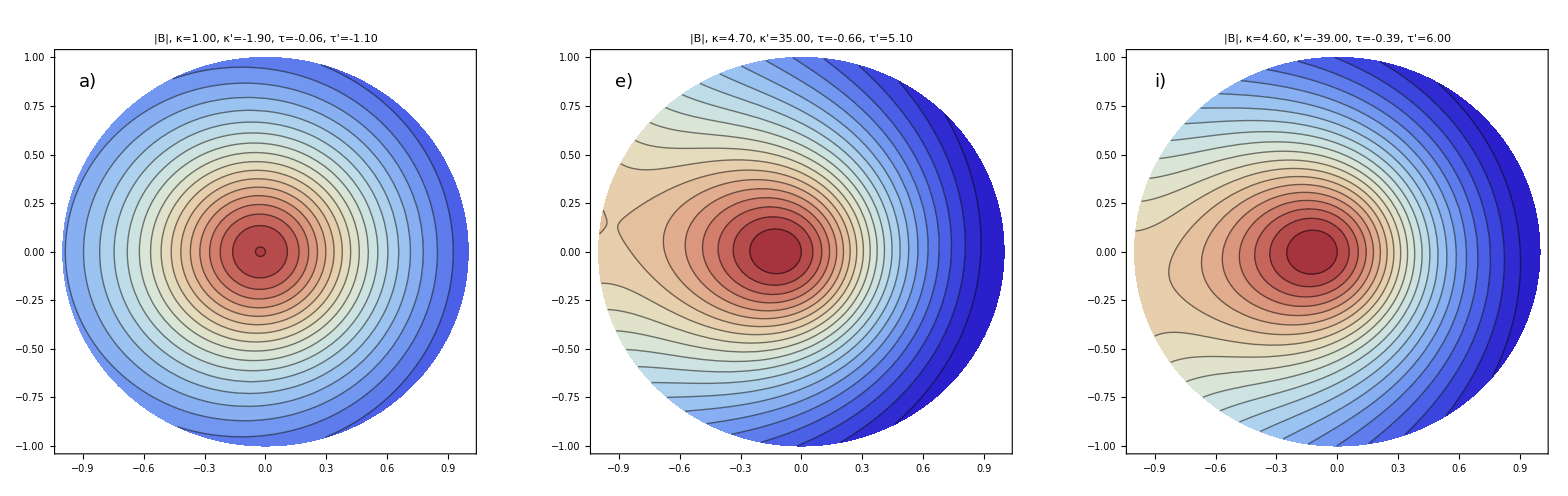

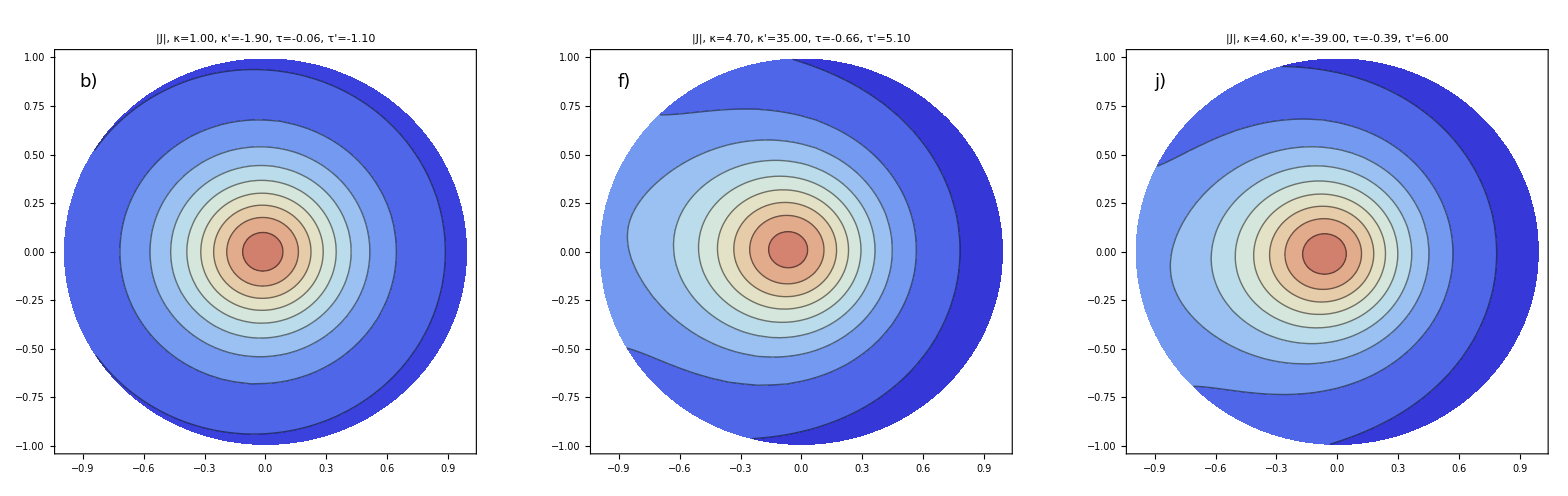

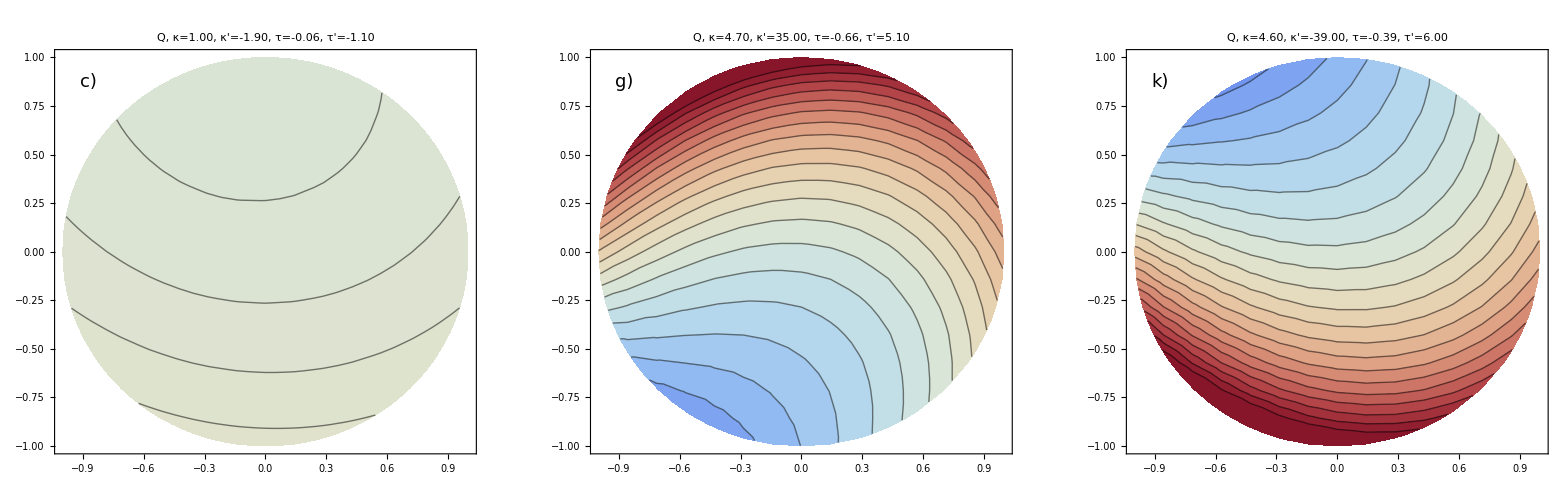

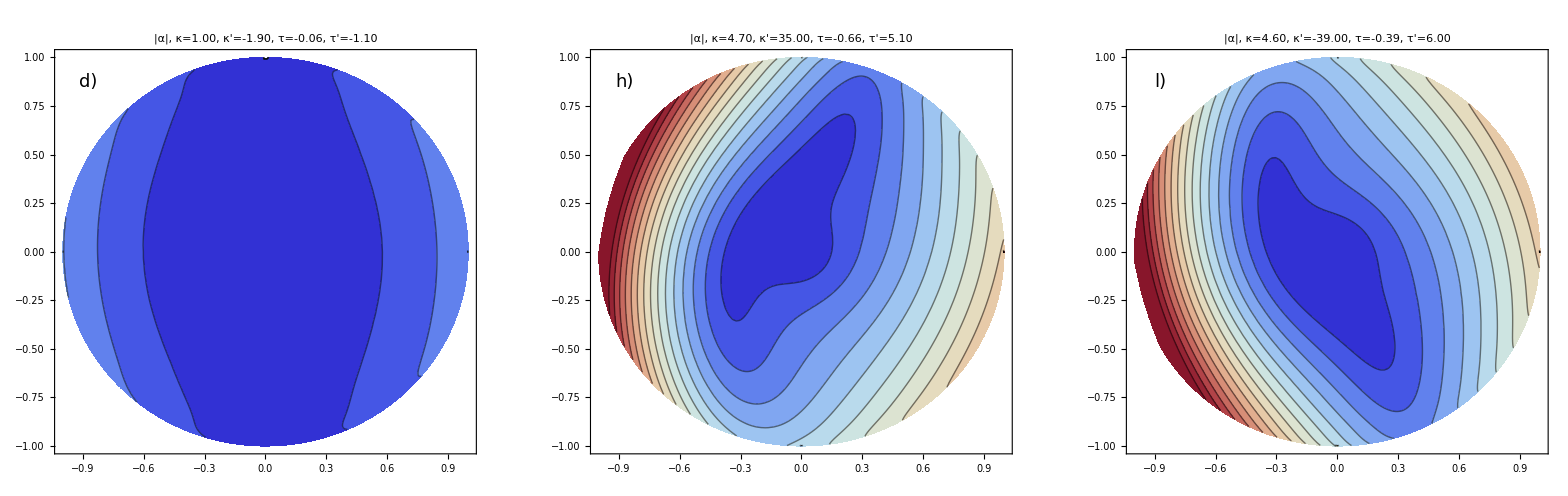

```mathematica
StringFunc[s_]:="κ="<>ToString[NumberForm[Eκ[s]//N,{2,2}]]<>", κ'="<>ToString[NumberForm[D[Eκ[t]//ComplexExpand,t]/.t->s//Evaluate//N,{2,2}]]<>", τ="<>ToString[NumberForm[Eτ[s]//N,{2,2}]]<>", τ'="<>ToString[NumberForm[D[Eτ[t]//ComplexExpand,t]/.t->s//Evaluate//N,{2,2}]]
BTwist=(r σ Subscript[FSB, φ][r,s,φ]+r σ τ[s] Subscript[FSB, s][r,s,φ])/(r(1+r σ κ[s] Cos[φ])Subscript[FSB, s][r,s,φ])/.l[s]->1/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords/.p1[t] -> Sqrt[x^2+y^2] /.p3[t] -> ArcTan[x, y];
BJAlign=180/Pi ArcSin[Norm[Bv[r,s,φ]×Jv[r,s,φ]]/Norm[Bv[r,s,φ]]/Norm[Jv[r,s,φ]]]/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords/.p1[t] -> Sqrt[x^2+y^2] /.p3[t] -> ArcTan[x, y];

CSB=GraphicsRow[{
ContourPlot[
Norm[Bv[r,s,φ]]/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords/.p1[t] -> Sqrt[x^2+y^2] /.p3[t] -> ArcTan[x, y]/.p2[t]->0//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[5, 16,0.5], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{5,16}}],ColorFunctionScaling->False,PlotLabel->"|B|, "<>StringFunc[0], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["a)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
ContourPlot[
Norm[Bv[r,s,φ]]/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords/.p1[t] -> Sqrt[x^2+y^2] /.p3[t] -> ArcTan[x, y]/.p2[t]->0.75//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[5, 16,0.5], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{5,16}}],ColorFunctionScaling->False,PlotLabel->"|B|, "<>StringFunc[0.75], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["e)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
ContourPlot[
Norm[Bv[r,s,φ]]/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords/.p1[t] -> Sqrt[x^2+y^2] /.p3[t] -> ArcTan[x, y]/.p2[t]->0.8//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[5, 16,0.5], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{5,16}}],ColorFunctionScaling->False,PlotLabel->"|B|, "<>StringFunc[0.8], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["i)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
BarLegend[{"ThermometerColors",{5,16}},Range[5, 16,1],LegendMargins->0,LegendLabel->"B [nT]",LabelStyle->{FontSize->16,FontColor->Black},LegendMarkerSize->350]
},ImageSize->1600,Alignment->Left
]
CSJ=GraphicsRow[{
ContourPlot[
Norm[Jv[r,s,φ]]/1.256/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords/.p1[t] -> Sqrt[x^2+y^2] /.p3[t] -> ArcTan[x, y]/.p2[t]->0//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0,600,50], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0,600}}],ColorFunctionScaling->False,PlotLabel->"|J|, "<>StringFunc[0], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["b)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
ContourPlot[
Norm[Jv[r,s,φ]]/1.256/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords/.p1[t] -> Sqrt[x^2+y^2] /.p3[t] -> ArcTan[x, y]/.p2[t]->0.75//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0,600,50], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0,600}}],ColorFunctionScaling->False,PlotLabel->"|J|, "<>StringFunc[0.75], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["f)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
ContourPlot[
Norm[Jv[r,s,φ]]/1.256/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.RCoords/.p1[t] -> Sqrt[x^2+y^2] /.p3[t] -> ArcTan[x, y]/.p2[t]->0.8//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0,600,50], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0,600}}],ColorFunctionScaling->False,PlotLabel->"|J|, "<>StringFunc[0.8], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["j)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
BarLegend[{"ThermometerColors",{0,600}},Range[0, 600,50],LegendMargins->0,LegendLabel->"J [nA/m^2]",LabelStyle->{FontSize->16,FontColor->Black},LegendMarkerSize->350]
},ImageSize->1600,Alignment->Left
]
CST=GraphicsRow[{
ContourPlot[
BTwist/.p2[t]->0//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[1.4, 2.6,0.01], MaxRecursion->1, ColorFunction->ColorData[{"ThermometerColors",{1.4, 2.6}}],ColorFunctionScaling->False,PlotLabel->"Q, "<>StringFunc[0], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["c)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
ContourPlot[
BTwist/.p2[t]->0.75//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[1.4, 2.6,0.05], MaxRecursion->0, ColorFunction->ColorData[{"ThermometerColors",{1.4, 2.6}}],ColorFunctionScaling->False,PlotLabel->"Q, "<>StringFunc[0.75], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["g)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
ContourPlot[
BTwist/.p2[t]->0.8//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[1.4, 2.6,0.05], MaxRecursion->0, ColorFunction->ColorData[{"ThermometerColors",{1.4, 2.6}}],ColorFunctionScaling->False,PlotLabel->"Q, "<>StringFunc[0.8], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["k)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
BarLegend[{"ThermometerColors",{1.4, 2.6}},Range[1.4, 2.6,0.05],LegendMargins->0,LegendLabel->"Q",LabelStyle->{FontSize->16,FontColor->Black},LegendMarkerSize->350]
},ImageSize->1600,Alignment->Left
]
CSJxB=GraphicsRow[{
ContourPlot[
BJAlign/.p2[t]->0//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0, 30,2], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0, 30}}],ColorFunctionScaling->False,PlotLabel->"|α|, "<>StringFunc[0.], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["d)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
ContourPlot[
BJAlign/.p2[t]->0.75//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0, 30,2], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0, 30}}],ColorFunctionScaling->False,PlotLabel->"|α|, "<>StringFunc[0.75], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["h)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
ContourPlot[
BJAlign/.p2[t]->0.8//Evaluate,
{x, -1, 1}, {y, -1, +1}, RegionFunction->Function[{x, y}, x^2 + y^2 <1 ], Contours->Range[0, 30,2], MaxRecursion->2, ColorFunction->ColorData[{"ThermometerColors",{0, 30}}],ColorFunctionScaling->False,PlotLabel->"|α|, "<>StringFunc[0.8], ImageSize->{400,400},ContourLabels->None,LabelStyle->{FontSize->14,FontColor->Black},
Epilog->{Text[Style["l)",18],Scaled[{0.08,0.92}]]},ImageSize->Large,LabelStyle->{FontSize->24,FontColor->Black}
],
BarLegend[{"ThermometerColors",{0,30}},Range[0, 30,2],LegendMargins->0,LegendLabel->"α [deg]",LabelStyle->{FontSize->16,FontColor->Black},LegendMarkerSize->350]
},ImageSize->1600,Alignment->Left
]
```

## Net Lorentz Force Vectors

```mathematica
If[Length[IntegralTermsReplacementRulesResult]>0,
FRP=(FSsqg[r,s,φ]Subscript[FSϵ, r][r,s,φ]Subscript[FSF, r][r,s,φ]/.SetZeroAFunc//Expand)/.IntegralTermsNullRulesResult/.IntegralTermsReplacementRulesResult;
FSP=(FSsqg[r,s,φ]Subscript[FSϵ, s][r,s,φ]Subscript[FSF, s][r,s,φ]/.SetZeroAFunc//Expand)/.IntegralTermsNullRulesResult/.IntegralTermsReplacementRulesResult;
FPP=(FSsqg[r,s,φ]Subscript[FSϵ, φ][r,s,φ]Subscript[FSF, φ][r,s,φ]/.SetZeroAFunc//Expand)/.IntegralTermsNullRulesResult/.IntegralTermsReplacementRulesResult;

FRPN=Coefficient[FRP//.ConfigGH//.ConfigGeneral,n[s]];
FRPB=Coefficient[FRP//.ConfigGH//.ConfigGeneral,b[s]];

FSPT=Coefficient[FSP//.ConfigGH//.ConfigGeneral,t[s]];
FSPN=Coefficient[FSP//.ConfigGH//.ConfigGeneral,b[s]];
FSPB=Coefficient[FSP//.ConfigGH//.ConfigGeneral,n[s]];

FPPN=Coefficient[FPP//.ConfigGH//.ConfigGeneral,n[s]];
FPPB=Coefficient[FPP//.ConfigGH//.ConfigGeneral,b[s]];
sVs=Range[0,1,.1];
FRNVs={};
FRBVs={};

FSTVs={};
FSNVs={};
FSBVs={};

FPNVs={};
FPBVs={};

For[i=1,i<Length[sVs],i++,
{
Print["Computing for s=",sVs[[i]]];
rnv=NIntegrate[FRPN/.ConfigE/.s->sVs[[i]]//Evaluate,{r,0,1},AccuracyGoal->10];
rbv=NIntegrate[FRPB/.ConfigE/.s->sVs[[i]]//Evaluate,{r,0,1},AccuracyGoal->10];

stv=NIntegrate[FSPT/.ConfigE/.s->sVs[[i]]//Evaluate,{r,0,1},AccuracyGoal->10];
snv=NIntegrate[FSPN/.ConfigE/.s->sVs[[i]]//Evaluate,{r,0,1},AccuracyGoal->10];
sbv=NIntegrate[FSPB/.ConfigE/.s->sVs[[i]]//Evaluate,{r,0,1},AccuracyGoal->10];

pnv=NIntegrate[FPPN/.ConfigE/.s->sVs[[i]]//Evaluate,{r,0,1},AccuracyGoal->10];
pbv=NIntegrate[FPPB/.ConfigE/.s->sVs[[i]]//Evaluate,{r,0,1},AccuracyGoal->10];

FRNVs=AppendTo[FRNVs,rnv];
FRBVs=AppendTo[FRBVs,rbv];

FSTVs=AppendTo[FSTVs,stv];
FSNVs=AppendTo[FSNVs,snv];
FSBVs=AppendTo[FSBVs,snv];

FPNVs=AppendTo[FPNVs,pnv];
FPBVs=AppendTo[FPBVs,pbv];
}
];

FArrows={};

For[i=1,i<Length[sVs],i++,{
Fvec=((FSTVs[[i]]) Et[s]+(FRNVs[[i]]+FSNVs[[i]]+FPNVs[[i]]) En[s]+(FRBVs[[i]]+FSBVs[[i]]+FPBVs[[i]]) Eb[s])/15;
FArrows=AppendTo[FArrows,Graphics3D[{Arrowheads[.02],Thickness[.005], Black,{Arrow[{Eγ[s],Eγ[s]+Fvec}/.s -> sVs[[i]] /. ConfigGeneral]}}]
];
FArrows=AppendTo[FArrows,Graphics3D[{Arrowheads[.01],Thickness[.002], Magenta,{Arrow[{Eγ[s],Eγ[s]+2.5σ En[s]}/.s -> sVs[[i]] /. ConfigGeneral]}}]
];
FArrows=AppendTo[FArrows,Graphics3D[{Arrowheads[.01],Thickness[.002], Orange,{Arrow[{Eγ[s],Eγ[s]+2.5σ  Eb[s]}/.s -> sVs[[i]] /. ConfigGeneral]}}]
];
}];

Show[
{
ParametricPlot3D[Er[s]/. ConfigGeneral /. r->1// Evaluate,{s,0,  1}, {φ, 0,2 Pi}, PlotStyle->{Opacity[0.1],Black}, Mesh-> {10, 0}],
FArrows
},
AxesLabel->{"X","Y","Z"}, Boxed->False,TicksStyle->Large,AxesStyle->Large,ViewPoint->{2, 4, 2.5},LabelStyle->Black,PlotRange->All
]
,Print["IntegralTermsReplacementRulesResult not defined (run appropriate Notebook)"]]
```

Computing for s=0.

Computing for s=0.1

Computing for s=0.2

Computing for s=0.3

Computing for s=0.4

Computing for s=0.5

Computing for s=0.6

Computing for s=0.7

Computing for s=0.8

Computing for s=0.9

-Graphics3D-

## Synthetic Profiles

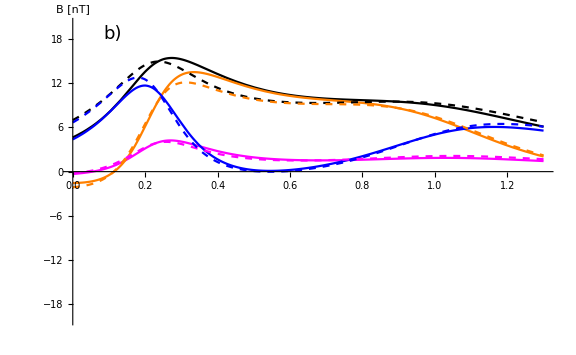

-Graphics3D-

```mathematica
Pf[repr_]:=Er[s]/.ConfigGeneral/.repr
Bfs[repr_]:=Bv[r,s,φ]/.SetZeroAFunc//.ConfigE//.ConfigGH//.ConfigGeneral/.repr
Bcyl[repr_]:=Bv[r,s,φ]/.SetZeroAFunc/.SetGeometryCylinder//.ConfigE//.ConfigGH//.ConfigGeneral/.repr

p1 =Er[s]/. ConfigGeneral /. r->0.2/.s->0.75/.φ->Pi;
p2 =Er[s]/. ConfigGeneral /. r->1/.s->0.6/.φ->Pi/4;
p[t_]:=p1+(p2-p1)t

p2b =Er[s]/. ConfigGeneral /. r->0/.s->0.72/.φ->0;
p1b =Er[s]/. ConfigGeneral /. r->1/.s->0.74/.φ->Pi/5;
pb[t_]:=p1b+(p2b-p1b)t

coords = {};
tparams={};
trange=Range[-0.8,1.5,0.025];
For[i=1,i<Length[trange],i++,
{
sol=NMinimize[{Norm[(Er[s]-p[trange[[i]]]/. ConfigGeneral)]//Evaluate,r∈PositiveReals,s∈PositiveReals,0<=φ<2Pi} ,{r,s,φ},Method->"DifferentialEvolution"];
If[(r<1/.sol[[2]]) && (sol[[1]]<0.001),coords=AppendTo[coords,sol[[2]]]; tparams=AppendTo[tparams,trange[[i]]]];
}
]

fx=Interpolation[{tparams,Thread[Bfs[coords]][[1]]}//Transpose,InterpolationOrder->3];
fy=Interpolation[{tparams,Thread[Bfs[coords]][[2]]}//Transpose,InterpolationOrder->3];
fz=Interpolation[{tparams,Thread[Bfs[coords]][[3]]}//Transpose,InterpolationOrder->3];
fxt=Interpolation[{tparams,Thread[Bcyl[coords]][[1]]}//Transpose,InterpolationOrder->3];
fyt=Interpolation[{tparams,Thread[Bcyl[coords]][[2]]}//Transpose,InterpolationOrder->3];
fzt=Interpolation[{tparams,Thread[Bcyl[coords]][[3]]}//Transpose,InterpolationOrder->3];

coordsb = {};
tparamsb={};
trangeb=Range[-1.5,2.5,0.05];
For[i=1,i<Length[trangeb],i++,
{
solb=NMinimize[{Norm[(Er[s]-pb[trangeb[[i]]]/. ConfigGeneral)]//Evaluate,r∈PositiveReals,s∈PositiveReals,0<=φ<2Pi} ,{r,s,φ},Method->"DifferentialEvolution"];
If[(r<1/.solb[[2]]) && (solb[[1]]<0.001),coordsb=AppendTo[coordsb,solb[[2]]]; tparamsb=AppendTo[tparamsb,trangeb[[i]]]];
}
]

fxb=Interpolation[{tparamsb,Thread[Bfs[coordsb]][[1]]}//Transpose,InterpolationOrder->3];
fyb=Interpolation[{tparamsb,Thread[Bfs[coordsb]][[2]]}//Transpose,InterpolationOrder->3];
fzb=Interpolation[{tparamsb,Thread[Bfs[coordsb]][[3]]}//Transpose,InterpolationOrder->3];
fxbt=Interpolation[{tparamsb,Thread[Bcyl[coordsb]][[1]]}//Transpose,InterpolationOrder->3];
fybt=Interpolation[{tparamsb,Thread[Bcyl[coordsb]][[2]]}//Transpose,InterpolationOrder->3];
fzbt=Interpolation[{tparamsb,Thread[Bcyl[coordsb]][[3]]}//Transpose,InterpolationOrder->3];

GraphicsRow[
{
Plot[{
Norm[{fxb[t+Min[tparamsb]],fyb[t+Min[tparamsb]],fzb[t+Min[tparamsb]]}],
fxb[t+Min[tparamsb]],fyb[t+Min[tparamsb]],fzb[t+Min[tparamsb]],
Norm[{fxbt[t+Min[tparamsb]],fybt[t+Min[tparamsb]],fzbt[t+Min[tparamsb]]}],
fxbt[t+Min[tparamsb]],fybt[t+Min[tparamsb]],fzbt[t+Min[tparamsb]]
},{t,0,Max[tparamsb]-Min[tparamsb]},PlotRange->{- 20,20},PlotStyle->{Black,Magenta,Orange,Blue,{Dashed,Black},{Dashed,Magenta},{Dashed,Orange},{Dashed,Blue}},AxesLabel->{"","B [nT]"},PlotLegends->{"B_T","B_X","B_Y","B_Z"},Epilog->{Text[Style["a)",18],Scaled[{0.1,0.95}]]},ImageSize->Large,LabelStyle->{FontSize->14,FontColor->Black}],
Plot[{
Norm[{fx[t+Min[tparams]],fy[t+Min[tparams]],fz[t+Min[tparams]]}],
fx[t+Min[tparams]],fy[t+Min[tparams]],fz[t+Min[tparams]],
Norm[{fxt[t+Min[tparams]],fyt[t+Min[tparams]],fzt[t+Min[tparams]]}],
fxt[t+Min[tparams]],fyt[t+Min[tparams]],fzt[t+Min[tparams]]
},{t,0,Max[tparams]-Min[tparams]},PlotRange->{-20,20},PlotStyle->{Black,Magenta,Orange,Blue,{Dashed,Black},{Dashed,Magenta},{Dashed,Orange},{Dashed,Blue}},AxesLabel->{"","B [nT]"},
Epilog->{Text[Style["b)",18],Scaled[{0.1,0.95}]]},ImageSize->Large,LabelStyle->{FontSize->14,FontColor->Black}]

},ImageSize->1400
]

Show[
{
ParametricPlot3D[Eγ[s]/. ConfigGeneral // Evaluate,{s,.5, 1}, PlotStyle->{Opacity[1],Blue, Thickness[.004]}],
ParametricPlot3D[Er[s]/. ConfigGeneral /. r->1// Evaluate,{s,.5,1}, {φ, 0,2Pi }, PlotStyle->{Opacity[0.15],Black}, Mesh-> {10, 0}],
Graphics3D[Text[Style["b)",18],p[-1]+{.12,0,0}]],
Graphics3D[Text[Style["a)",18],pb[-2.5]+{-.1,0,0}]],
Graphics3D[{PointSize[0.02],Point[p[t]/.t->-1.5]}],Graphics3D[{PointSize[0.02],Point[pb[t]/.t->-2]}],
Graphics3D[{Arrowheads[.035],Thickness[.005],Arrow[{p[t]/.t->-1.5,p[t]/.t->2}]}],
Graphics3D[{Arrowheads[.035],Thickness[.005],Arrow[{pb[t]/.t->-2,pb[t]/.t->4}]}]
},
AxesLabel->{"X","Y","Z"}, Boxed->False,TicksStyle->Large,AxesStyle->None,ViewPoint->{2, -4, 2.5},LabelStyle->Black,PlotRange->All,Axes->False
]
```